{{u→Function[{t},-1/(7 (-1+√7 π-2 π^2) (1+√7 π+2 π^2))ⅇ^(-t/2) (14 π Cos[(√7 t)/2]-√7 ⅇ^(t/2) Cos[(√7 t)/2] Cos[1/2 (√7-4 π) t]-7 ⅇ^(t/2) π Cos[(√7 t)/2] Cos[1/2 (√7-4 π) t]-2 √7 ⅇ^(t/2) π^2 Cos[(√7 t)/2] Cos[1/2 (√7-4 π) t]+√7 ⅇ^(t/2) Cos[(√7 t)/2] Cos[1/2 (√7+4 π) t]-7 ⅇ^(t/2) π Cos[(√7 t)/2] Cos[1/2 (√7+4 π) t]+2 √7 ⅇ^(t/2) π^2 Cos[(√7 t)/2] Cos[1/2 (√7+4 π) t]-6 √7 π Sin[(√7 t)/2]+16 √7 π^3 Sin[(√7 t)/2]+7 ⅇ^(t/2) Cos[1/2 (√7-4 π) t] Sin[(√7 t)/2]+3 √7 ⅇ^(t/2) π Cos[1/2 (√7-4 π) t] Sin[(√7 t)/2]-14 ⅇ^(t/2) π^2 Cos[1/2 (√7-4 π) t] Sin[(√7 t)/2]-8 √7 ⅇ^(t/2) π^3 Cos[1/2 (√7-4 π) t] Sin[(√7 t)/2]-7 ⅇ^(t/2) Cos[1/2 (√7+4 π) t] Sin[(√7 t)/2]+3 √7 ⅇ^(t/2) π Cos[1/2 (√7+4 π) t] Sin[(√7 t)/2]+14 ⅇ^(t/2) π^2 Cos[1/2 (√7+4 π) t] Sin[(√7 t)/2]-8 √7 ⅇ^(t/2) π^3 Cos[1/2 (√7+4 π) t] Sin[(√7 t)/2]-7 ⅇ^(t/2) Cos[(√7 t)/2] Sin[1/2 (√7-4 π) t]-3 √7 ⅇ^(t/2) π Cos[(√7 t)/2] Sin[1/2 (√7-4 π) t]+14 ⅇ^(t/2) π^2 Cos[(√7 t)/2] Sin[1/2 (√7-4 π) t]+8 √7 ⅇ^(t/2) π^3 Cos[(√7 t)/2] Sin[1/2 (√7-4 π) t]-√7 ⅇ^(t/2) Sin[(√7 t)/2] Sin[1/2 (√7-4 π) t]-7 ⅇ^(t/2) π Sin[(√7 t)/2] Sin[1/2 (√7-4 π) t]-2 √7 ⅇ^(t/2) π^2 Sin[(√7 t)/2] Sin[1/2 (√7-4 π) t]+7 ⅇ^(t/2) Cos[(√7 t)/2] Sin[1/2 (√7+4 π) t]-3 √7 ⅇ^(t/2) π Cos[(√7 t)/2] Sin[1/2 (√7+4 π) t]-14 ⅇ^(t/2) π^2 Cos[(√7 t)/2] Sin[1/2 (√7+4 π) t]+8 √7 ⅇ^(t/2) π^3 Cos[(√7 t)/2] Sin[1/2 (√7+4 π) t]+√7 ⅇ^(t/2) Sin[(√7 t)/2] Sin[1/2 (√7+4 π) t]-7 ⅇ^(t/2) π Sin[(√7 t)/2] Sin[1/2 (√7+4 π) t]+2 √7 ⅇ^(t/2) π^2 Sin[(√7 t)/2] Sin[1/2 (√7+4 π) t])]}}

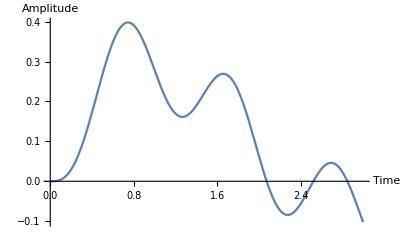

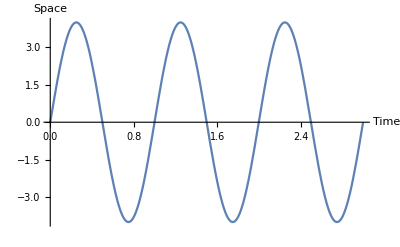

{t,u,f}

C:\Users\Razer\OneDrive - Technische Universität Graz\Dokumente\Uni\6.Semester\BAC\Code_bac\PI_GP_regressor\data_files\damped_m1k2b1.csv

```mathematica
L=1;
f[t_]:= Sin[2*Pi*t]*4;
m=1;
gamma=1;
k=2;
tm = 3;
eqn=m*D[u[t],{t,2}]+gamma*D[u[t],{t,1}]+k*u[t]==f[t];

initialConditions={u[0]==0,Derivative[1][u][0]==0};

sol=DSolve[{eqn,initialConditions},u,t]

Plot[Evaluate[u[t]/. sol],{t,0,tm},AxesLabel->{"Time","Amplitude"}]
Plot[Evaluate[f[t]], {t,0,tm},AxesLabel->{"Time","Space","Amplitude"}]
soln=u[t]/. First@sol;(*This applies the rules from sol to u[t]*)
data=Table[{tval,soln/. t->tval,f[tval]},{tval,0,tm,0.01}];(*This replaces each t in soln and f with the actual values*)
header = {"t","u","f"}
filename="C:\\Users\\Razer\\OneDrive - Technische Universität Graz\\Dokumente\\Uni\\6.Semester\\BAC\\Code_bac\\PI_GP_regressor\\data_files\\damped_m1k2b1.csv";
If[FileExistsQ[filename],DeleteFile[filename]];
CreateFile[filename];
dataWithHeader=Prepend[data,header];
Export[filename, dataWithHeader]
```

{{u→Function[{t},1/((4+81 π^4) (4+625 π^4))2 ⅇ^-t (16 π Cos[t]-2940 π^5 Cos[t]+24 ⅇ^t π Cos[t]^2 Cos[3 π t]+3750 ⅇ^t π^5 Cos[t]^2 Cos[3 π t]-40 ⅇ^t π Cos[t]^2 Cos[5 π t]-810 ⅇ^t π^5 Cos[t]^2 Cos[5 π t]+392 π^3 Sin[t]-6750 π^7 Sin[t]+24 ⅇ^t π Cos[3 π t] Sin[t]^2+3750 ⅇ^t π^5 Cos[3 π t] Sin[t]^2-40 ⅇ^t π Cos[5 π t] Sin[t]^2-810 ⅇ^t π^5 Cos[5 π t] Sin[t]^2-8 ⅇ^t Cos[t]^2 Sin[3 π t]+36 ⅇ^t π^2 Cos[t]^2 Sin[3 π t]-1250 ⅇ^t π^4 Cos[t]^2 Sin[3 π t]+5625 ⅇ^t π^6 Cos[t]^2 Sin[3 π t]-8 ⅇ^t Sin[t]^2 Sin[3 π t]+36 ⅇ^t π^2 Sin[t]^2 Sin[3 π t]-1250 ⅇ^t π^4 Sin[t]^2 Sin[3 π t]+5625 ⅇ^t π^6 Sin[t]^2 Sin[3 π t]+8 ⅇ^t Cos[t]^2 Sin[5 π t]-100 ⅇ^t π^2 Cos[t]^2 Sin[5 π t]+162 ⅇ^t π^4 Cos[t]^2 Sin[5 π t]-2025 ⅇ^t π^6 Cos[t]^2 Sin[5 π t]+8 ⅇ^t Sin[t]^2 Sin[5 π t]-100 ⅇ^t π^2 Sin[t]^2 Sin[5 π t]+162 ⅇ^t π^4 Sin[t]^2 Sin[5 π t]-2025 ⅇ^t π^6 Sin[t]^2 Sin[5 π t])]}}

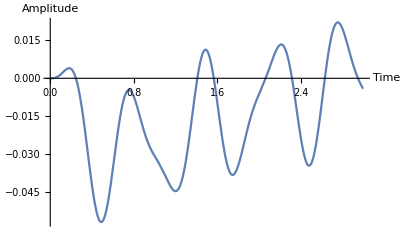

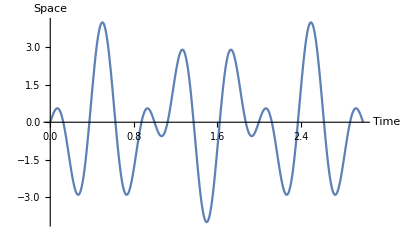

{t,u,f}

C:\Users\Razer\OneDrive - Technische Universität Graz\Dokumente\Uni\6.Semester\BAC\Code_bac\PI_GP_regressor\data_files\damped_second.csv

```mathematica
L=1;
f[t_]:= Sin[Pi*t]*4*Cos[4*Pi*t];
m=1;
gamma=2;
k=2;
tm = 3;
eqn=m*D[u[t],{t,2}]+gamma*D[u[t],{t,1}]+k*u[t]==f[t];

initialConditions={u[0]==0,Derivative[1][u][0]==0};

sol=DSolve[{eqn,initialConditions},u,t]

Plot[Evaluate[u[t]/. sol],{t,0,tm},AxesLabel->{"Time","Amplitude"}]
Plot[Evaluate[f[t]], {t,0,tm},AxesLabel->{"Time","Space","Amplitude"}]
soln=u[t]/. First@sol;(*This applies the rules from sol to u[t]*)
data=Table[{tval,soln/. t->tval,f[tval]},{tval,0,tm,0.01}];(*This replaces each t in soln and f with the actual values*)
header = {"t","u","f"}
filename="C:\\Users\\Razer\\OneDrive - Technische Universität Graz\\Dokumente\\Uni\\6.Semester\\BAC\\Code_bac\\PI_GP_regressor\\data_files\\damped_second.csv";
If[FileExistsQ[filename],DeleteFile[filename]];
CreateFile[filename];
dataWithHeader=Prepend[data,header];
Export[filename, dataWithHeader]
```

{{u→InterpolatingFunction[…]}}

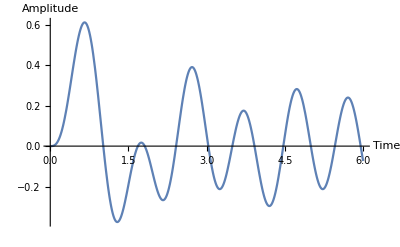

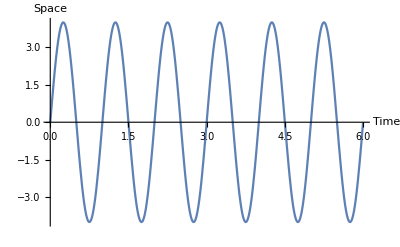

{t,u,f}

C:\Users\Razer\OneDrive - Technische Universität Graz\Dokumente\Uni\6.Semester\BAC\Code_bac\PI_GP_regressor\data_files\damped_third.csv

```mathematica
L=1;
f[t_]:= Sin[2*Pi*t]*4;
m=0.5;
gamma=0.5;
k=4;
tm = 6;
eqn=m*D[u[t],{t,2}]+gamma*D[u[t],{t,1}]+k*u[t]==f[t];

initialConditions={u[0]==0,Derivative[1][u][0]==0};

sol=NDSolve[{eqn,initialConditions},u,{t,0,tm}]

Plot[Evaluate[u[t]/. sol],{t,0,tm},AxesLabel->{"Time","Amplitude"}]
Plot[Evaluate[f[t]], {t,0,tm},AxesLabel->{"Time","Space","Amplitude"}]
soln=u[t]/. First@sol;(*This applies the rules from sol to u[t]*)
data=Table[{tval,soln/. t->tval,f[tval]},{tval,0,tm,0.01}];(*This replaces each t in soln and f with the actual values*)
header = {"t","u","f"}
filename="C:\\Users\\Razer\\OneDrive - Technische Universität Graz\\Dokumente\\Uni\\6.Semester\\BAC\\Code_bac\\PI_GP_regressor\\data_files\\damped_third.csv";
If[FileExistsQ[filename],DeleteFile[filename]];
CreateFile[filename];
dataWithHeader=Prepend[data,header];
Export[filename, dataWithHeader]
```